```mathematica
SetDirectory["/Volumes/MicroSD/2_PostDoc_SD/CaCO3/Common_Tangent-master"]
oneDat=Import["1.dat"][[2;;-1]]
twoDat=Import["2.dat"][[2;;-1]]
```

/Volumes/MicroSD/2_PostDoc_SD/CaCO3/Common_Tangent-master

{{61.6634,-941.255},{62.3429,-941.255},{62.9227,-941.255},{63.0043,-941.255},{63.716,-941.255},{64.4085,-941.255},{65.1047,-941.254},{65.805,-941.254},{66.5094,-941.253},{67.2181,-941.253},{67.9312,-941.252}}

{{54.6569,-941.248},{55.3555,-941.249},{56.1392,-941.25},{56.9292,-941.251},{57.6993,-941.252},{58.4712,-941.253},{59.2667,-941.254},{60.0548,-941.254},{60.8627,-941.254}}

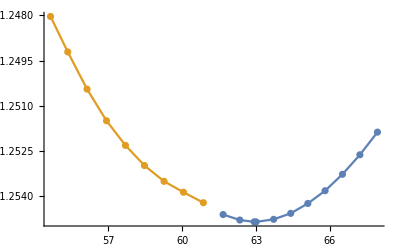

```mathematica
Show[ListLinePlot@{oneDat,twoDat},ListPlot@{oneDat,twoDat}]
```

```mathematica
ClearAll@x
```

```mathematica
fitOneDatx=Fit[oneDat,{1,x,x^2,x^3},x]
fitTwoDatx=Fit[twoDat,{1,x,x^2,x^3},x]
fitOneDat=fitOneDatx/.x->y
fitTwoDat=fitTwoDatx/.x->z
```

-939.849-0.0583396 x+0.000789491 x^2-3.45387×10^-6 x^3

-939.815-0.0652345 x+0.000982731 x^2-4.91953×10^-6 x^3

-939.849-0.0583396 y+0.000789491 y^2-3.45387×10^-6 y^3

-939.815-0.0652345 z+0.000982731 z^2-4.91953×10^-6 z^3

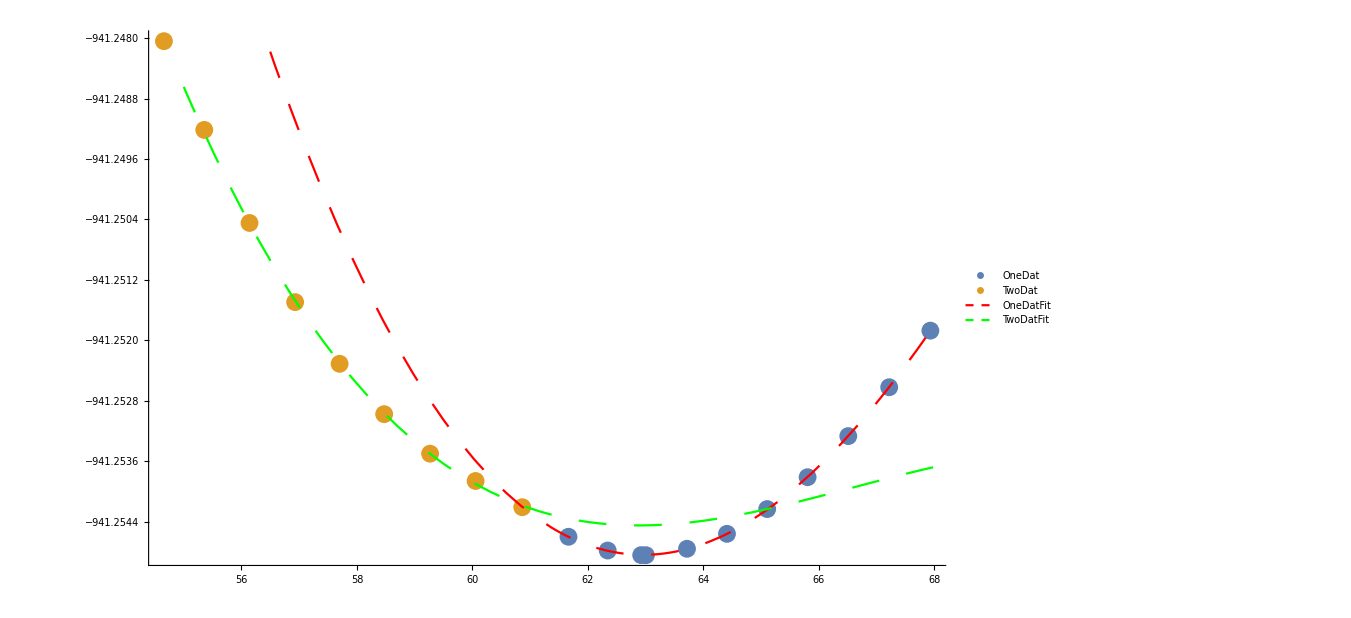

```mathematica
Show[ListPlot[{oneDat,twoDat},PlotLegends->{"OneDat","TwoDat"}],Plot[fitOneDatx,{x,55,68},PlotStyle->Directive[Dashing[0.02],Red],PlotLegends->{"OneDatFit"}],Plot[fitTwoDatx,{x,55,68},PlotStyle->Directive[Dashing[0.02],Green],PlotLegends->{"TwoDatFit"}],ImageSize->1000]
```

```mathematica
fitOneDat
fitOneDatDash=D[fitOneDat,y]
fitTwoDat
fitTwoDatDash=D[fitTwoDat,z]
```

-939.849-0.0583396 y+0.000789491 y^2-3.45387×10^-6 y^3

-0.0583396+0.00157898 y-0.0000103616 y^2

-939.815-0.0652345 z+0.000982731 z^2-4.91953×10^-6 z^3

-0.0652345+0.00196546 z-0.0000147586 z^2

```mathematica
sol=Solve[{(fitOneDat-fitTwoDat)/(y-z)==fitTwoDatDash&&(fitOneDat-fitTwoDat)/(y-z)==fitOneDatDash},{y,z},Reals]
solConditions=Solve[{(fitOneDat-fitTwoDat)/(y-z)==fitTwoDatDash&&(fitOneDat-fitTwoDat)/(y-z)==fitOneDatDash&&56<z<64&&56<y<64},{y,z},Reals]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{y→4.36525,z→7.31639},{y→5.90593,z→5.90593},{y→60.8115,z→60.8115},{y→61.4458,z→59.9939},{y→65.1271,z→65.1271}}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{y→60.8115,z→60.8115},{y→61.4458,z→59.9939}}

```mathematica
solConditions[[2]]
```

{y→61.4458,z→59.9939}

```mathematica
a=fitTwoDat/.solConditions[[2]]
b=-fitOneDatDash*z/.solConditions[[2]]
c=(fitOneDatDash/.solConditions[[2]])*x
commonTangent=a+b+c
```

-941.254

0.0263296

-0.000438871 x

-941.228-0.000438871 x

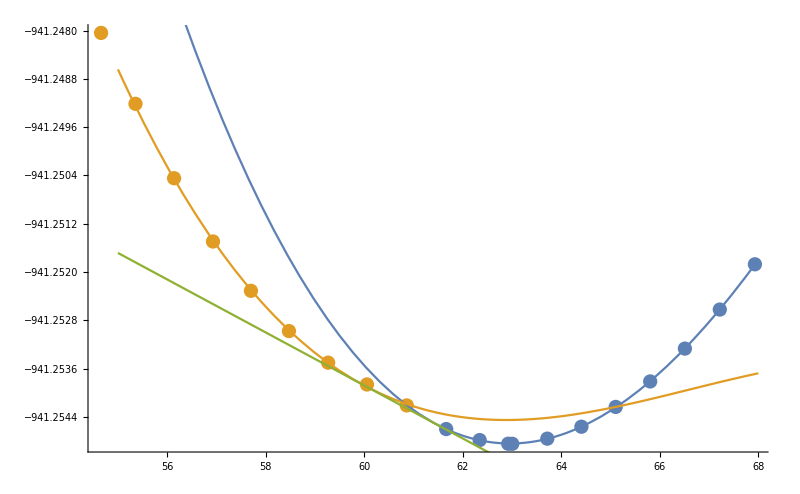

```mathematica
Show[ListPlot[{oneDat,twoDat}],Plot[{fitOneDatx,fitTwoDatx,commonTangent},{x,55,68}],ImageSize->800]
```